## Preamble

### Units and constants

```mathematica
$Assumptions={GeV>0};
Kg =N[ 5.6096 10^26]GeV; Gram = 10^-3 Kg;
Meter = N[1/(0.1973 10^-15)] GeV^-1;CentiMeter = 10^-2 Meter;
Second = N[299792458] Meter; Hz = Second^-1;
Hour = 3600 Second;Year = 365 24 Hour;
Kelvin = 8.6 10^-5 eV;
Joule = Kg Meter^2 Second^-2; erg = 10^-7 Joule; Watt = Joule Second^-1;
Newton = Kg Meter Second^-2;
Tesla =N[195] eV^2;Gauss=10^-4 Tesla;
ElectronCharge  = 0.303;
Volt = eV/ElectronCharge;
MProton = 0.938 GeV;
MElectron = 511.keV;
MMuon =105.6583745MeV;
MTau=1776.86MeV;
MPion=0.13957018GeV;
MQuarkUp = 2.01 MeV;
MQuarkDown = 4.79MeV;
MZboson=91.1876GeV;MWboson=80.379 GeV;MHiggs=125.18 GeV;
Coulomb = (5.28 10^-19)^-1;
MuNuclear = ElectronCharge/(2 MProton); MuBohr = ElectronCharge/(2MElectron); BohrRadius = 1/(AlphaEM MElectron);
Debye = 3.33564 10^-30 Coulomb Meter; Angstrom  =10^-10 Meter;
barn = 10^-28 Meter^2; fb = 10^-15 barn;
Ampere = Coulomb/Second; Ohm = Volt/Ampere; Farad = Coulomb/Volt; Henry = Joule/Ampere^2;
Subscript[G, F]=N[1.166 10^-5] GeV^-2;
AlphaEM = 1/137;
MPlanck = 1.2209×10^19 GeV; GN = MPlanck^-2;
mPlanck = MPlanck/√(8π);
meV = 10^-3 eV; eV = 10^-3 keV; keV =  10^-3 MeV; MeV= 10^-3 GeV;
Hubble0 = 67.8 10^3 Meter Second^-1 Mpc^-1; RhoCrit =(3 Hubble0^2)/(8π GN); hubble0 = Hubble0/(100 10^3 Meter Second^-1 Mpc^-1);
RhoCritOverhSq=1.05371 10^-5 GeV CentiMeter^-3;entropy0=Pi^4/(45*Zeta[3])(2+21/11)*410.7 CentiMeter^-3;
OmegaDM=0.12;
zeq = 3250;HubbleEq = Hubble0(1+zeq)^(3/2);aeq = N@(1/(1+zeq));
RhoDMU = 0.23 3/(8π)Hubble0^2 MPlanck^2;
RhoDMG = (0.4 GeV)/CentiMeter^3;
v0DM = 235 10^3 Meter Second^-1; σvDM = v0DM/√2;
kpc = 3261 Year; Mpc = 10^3 kpc;
pc = 10^-3 kpc;
AU = 150 10^6 10^3 Meter;
MSolar = 1.98 10^30 Kg;
MassEarth = 5.972 10^24 Kg;
MassMoon = 0.012300MassEarth;
MassDensityEarth = 5.59 Kg/(10CentiMeter)^3;
RadiusEarth = 6371 10^3 Meter;
NAvo = 6.022 10^23;
bar = 10^5 Newton Meter^-2;
Torr = 1/750.061683 bar;
nst = (1 bar)/(273.15Kelvin);
arcmin = (2π)/360 1/60;arcsec = (2π)/360 1/3600;mas = 10^-3 arcsec;muas = 10^-6 arcsec;
masy = 10^-3 arcsec Year^-1;muasy = 10^-6 arcsec Year^-1; muasyy = 10^-6 arcsec Year^-2;
Jy=10^-23 erg Second^-1 CentiMeter^-2 Hz^-1;
```

### Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$DataDir = "../data/";
$ListDir = "../lists/";
$FigDir = "../figs/";
```

### Plot options

```mathematica
fontsize=20;
plotstyle={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->500,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->"Times"(*Times*)],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->GoldenRatio^-1(*,PlotRangePadding->None*)};
plotstylelog={FrameTicksStyle->{{Black,Black},{Black,Black}},PlotRange->All,Background->White,ImageSize->500,GridLines->Automatic,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], Axes->False,AspectRatio->GoldenRatio^-1};
```

## Energy transition estimate

```mathematica
fcoeff[n_,l_,j_]:=2/n-(4(2+3l+3j(2l+1)))/((j+l)(j+l+1)(j+l+2))
hcoeff[l_,j_]:=16/((l+j)(l+j+1)(l+j+2))
Eoverμ[n_,l_,j_,m_,α_,χ_]:=1-α^2/(2 n^2)-α^4/(8 n^4)+fcoeff[n,l,j]/n^3 α^4+hcoeff[l,j]/n^3 χ m α^5
```

```mathematica
1/((Eoverμ[3,2,1,1,α,0.99]-Eoverμ[1,0,1,-1,α,0.99])*μ/.{α->0.01,μ->10^-12 eV})/(24Hour)
```

0.000171332

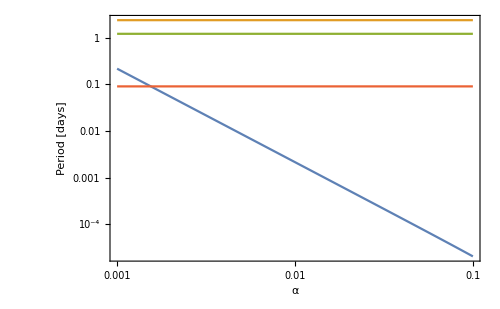

```mathematica
Block[{μ=5 10^-13 eV,ΔE},
ΔE=(Eoverμ[3,2,1,1,α,0.99]-Eoverμ[1,0,1,-1,α,0.99])*μ;
LogLogPlot[{2π/ΔE/(24Hour),2.35,1.2,0.09},{α,0.001,0.1},FrameLabel->{"α","Period [days]"},Evaluate@plotstyle]]
```

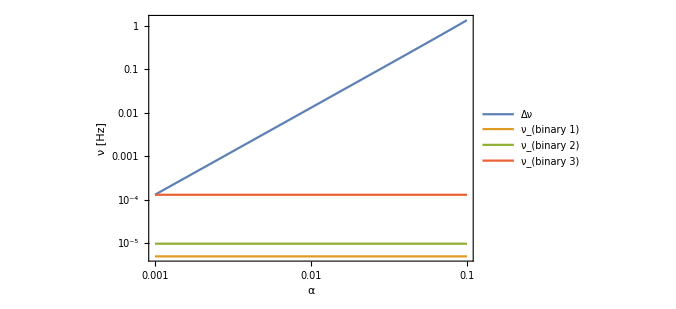

```mathematica
Block[{μ=1.2 10^-12 eV,χ=0.5,ΔE},
ΔE=(Eoverμ[3,2,1,1,α,χ]-Eoverμ[1,0,1,-1,α,χ])*μ/(2π);
LogLogPlot[{ΔE/Hz,1/(2.35 24 Hour)/Hz,1/(1.2 24 Hour)/Hz,1/(0.09 24 Hour)/Hz},{α,0.001,0.1},FrameLabel->{"α","ν [Hz]"},PlotLegends->Placed[{"Δν","ν_(binary 1)","ν_(binary 2)","ν_(binary 3)"},Right],Evaluate@plotstyle]]
```

{{1.28804×10^-12,1.46097×10^-12,1.42185×10^-12}}

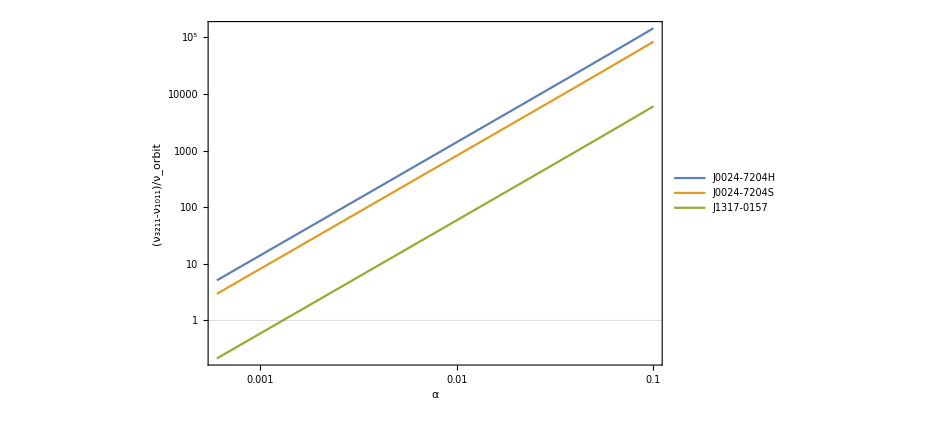

```mathematica
Block[{χ=0.5,ΔE},
Plist={2.35769689,1.201724200,0.089128297};
frotList={311.49,353.31,343.85};
ΔE=(Eoverμ[3,2,1,-1,α,χ]-Eoverμ[1,0,1,1,α,χ])/2;
Print[{2π# Hz/eV}&@frotList];
ratioList=Table[ΔE*frotList⟦i⟧Hz/(1/(Plist⟦i⟧ 24 Hour)),{i,1,3}];
LogLogPlot[ratioList,{α,0.0006,0.1},FrameLabel->{{"(ν_3211-ν_1011)/ν_orbit",""},{"α","Superradiance levels transition"}},GridLines->{{},{1}},PlotLegends->Placed[{"J0024-7204H","J0024-7204S","J1317-0157"},Right],ImageSize->700,Evaluate@plotstyle]]
```

## Accretion from surrounding

```mathematica
τacc[ϵ_,α_,μ_]:=(ϵ α^(-3/2)√0.1 MPlanck μ)/(π CentiMeter^-3)
```

```mathematica
τacc[10^-7,0.007451383181210485,2 10^-13 eV]/Year
```

103.83

```mathematica
τacc[10^-10,0.007451383181210485,2 10^-13 eV]/Year
```

0.10383

```mathematica
τacc[10^-7,0.04470829908726291,2 10^-13 eV]/(Year)
```

7.06475

```mathematica
τacc[10^-10,0.04470829908726291,2 10^-13 eV]/(3600Second)
```

61.8872

```mathematica
τacc[10^-7,0.07451383181210484,2 10^-13 eV]/Year
```

3.2834

```mathematica
τacc[10^-10,0.07451383181210484,2 10^-13 eV]/(3600Second)
```

28.7626

```mathematica
τacc[10^-7,0.44708299087262904,2 10^-13 eV]/(3600Second)
```

1957.04

```mathematica
τacc[10^-10,0.44708299087262904,2 10^-13 eV]/(3600Second)
```

1.95704

```mathematica
GN 5MSolar 2 10^-12 eV
```

0.0745138